```mathematica
(* Jose Dario Sanchez *)
(* josedario@ucla.edu *)
(*ID: 004-505-398 *)
(* Homeowork #4 *)
```

The following graphs plot position and velocity with step-sizes of 1*cycle, (1/3)*cycle, and (1/10)*cycle, respectively:

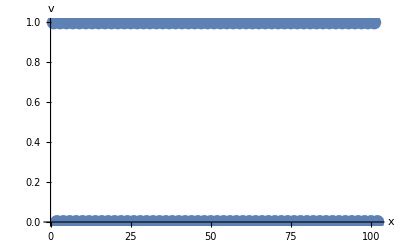
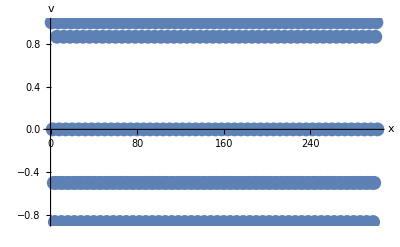
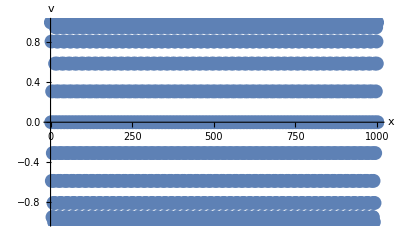

* Regularly spaced intervals here denote that the energy of the system is perfectly conserved.

```mathematica
Remove["Global`*"]

ω=1;
β=0;

cycle=2 π/ω;
tMin=0;
tMax=50*cycle;
tStep1=cycle;
tStep2=cycle/3;
tStep3=cycle/10;

oscEq=x''[t]+2*β*x'[t]+(ω^2)*x[t]==0;
x[t_]=DSolveValue[{oscEq,x[0]==1,x'[0]==0},x[t],t];

position=x[t];
velocity=x'[t];

xvPoints1=Table[{position,velocity},{t,tMin,tMax,tStep1}];
data1=Flatten[xvPoints1,1];

xvPoints2=Table[{position,velocity},{t,tMin,tMax,tStep2}];
data2=Flatten[xvPoints2,1];

xvPoints3=Table[{position,velocity},{t,tMin,tMax,tStep3}];
data3=Flatten[xvPoints3,1];

Print["The following graphs plot position and velocity with step-sizes of 1*cycle, (1/3)*cycle, and (1/10)*cycle, respectively:"]
{ListPlot[data1,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}],
ListPlot[data2,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}],
ListPlot[data3,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}]}
Print["* Regularly spaced intervals here denote that the energy of the system is perfectly conserved."]
```

The following graphs plot position and velocity with β1=0.9, β2=0.5, β3=0.1, respectively:

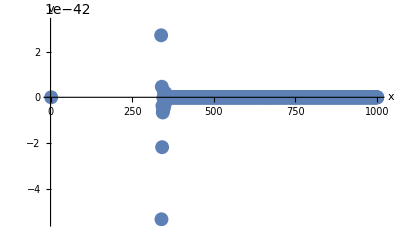
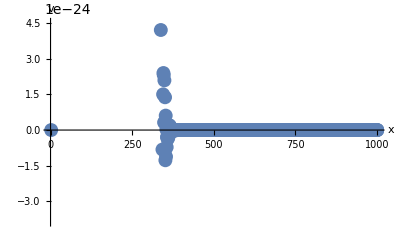
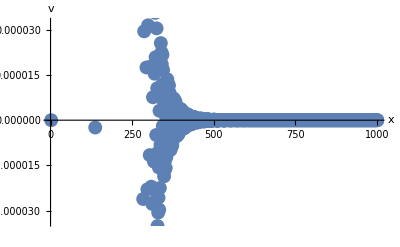

* The lower the β damping coefficient, the higher the variation of velocity near the x=400 mark.

```mathematica
ClearAll["Global`*"]

ω=1;
β1=0.9;
β2=0.5;
β3=0.1;

cycle=2 π/ω;
tMin=0;
tMax=50*cycle;
tStep=cycle/10;

dampedOscEq1=x''[t]+2*β1*x'[t]+(ω^2)*x[t]==0;
dampedOscEq2=y''[t]+2*β2*y'[t]+(ω^2)*y[t]==0;
dampedOscEq3=z''[t]+2*β3*z'[t]+(ω^2)*z[t]==0;

x[t_]=DSolveValue[{dampedOscEq1,x[0]==1,x'[0]==0},x[t],t];
y[t_]=DSolveValue[{dampedOscEq2,y[0]==1,y'[0]==0},y[t],t];
z[t_]=DSolveValue[{dampedOscEq3,z[0]==1,z'[0]==0},z[t],t];

position1=x[t];
velocity1=x'[t];
position2=y[t];
velocity2=y'[t];
position3=z[t];
velocity3=z'[t];

xvPoints1=Table[{position1,velocity1},{t,tMin,tMax,tStep}];
data1=Flatten[xvPoints1,1];

xvPoints2=Table[{position2,velocity2},{t,tMin,tMax,tStep}];
data2=Flatten[xvPoints2,1];

xvPoints3=Table[{position3,velocity3},{t,tMin,tMax,tStep}];
data3=Flatten[xvPoints3,1];

Print["The following graphs plot position and velocity with β1=0.9, β2=0.5, β3=0.1, respectively:"]
{ListPlot[data1,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}],
ListPlot[data2,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}],
ListPlot[data3,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}]}
Print["* The lower the β damping coefficient, the higher the variation of velocity near the x=400 mark."]
```

The following graphs plot position and velocity with intervals of 0<t<25 cycles and 25<t<50 cycles, respectively:

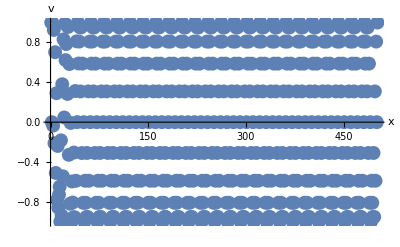
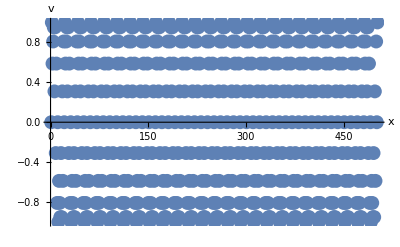

* There is some instability in the beginning of the first graph. The system has reached a steady rate of energy decay in the second graph.

```mathematica
ClearAll["Global`*"]

ω=1;
β=0.5;

cycle=2 π/ω;
tMin1=0;
tMax1=25*cycle;
tMin2=25*cycle;
tMax2=50*cycle;
tStep=cycle/10;

drivenOscEq=x''[t]+2*β*x'[t]+(ω^2)*x[t]==Cos[ω*t];
x[t_]=DSolveValue[{drivenOscEq,x[0]==1,x'[0]==0},x[t],t];

position=x[t];
velocity=x'[t];

xvPoints1=Table[{position,velocity},{t,tMin1,tMax1,tStep}];
data1=Flatten[xvPoints1,1];

xvPoints2=Table[{position,velocity},{t,tMin2,tMax2,tStep}];
data2=Flatten[xvPoints2,1];

Print["The following graphs plot position and velocity with intervals of 0<t<25 cycles and 25<t<50 cycles, respectively:"]
{ListPlot[data1,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}],
ListPlot[data2,PlotStyle->{PointSize[0.025]},AxesLabel->{"x","v"}]}
Print["* There is some instability in the beginning of the first graph. The system has reached a steady rate of energy decay in the second graph."]
```

```mathematica
(* The rest of the homework here is incomplete*)
```

```mathematica
Remove["Global`*"]

f=0.7;
c=0.05;
ω=0.3;

cycle=2 π/ω;
tMin=0;
tMax=50*cycle;
tStep=cycle;


oscDiffEq1=x'[τ]==y[τ];
oscDiffEq2=y'[τ]==-c*y[τ]-Sin[x[τ]]+f*Cos[ω*τ];
xFunction=ParametricNDSolveValue[oscDiffEq1,x[τ],τ]
yFunction=ParametricNDSolveValue[oscDiffEq2,y[τ],τ]
```

ParametricNDSolveValue::argm: ParametricNDSolveValue called with 3 arguments; 4 or more arguments are expected.

ParametricNDSolveValue[x'[τ]==y[τ],x[τ],τ]

ParametricNDSolveValue::argm: ParametricNDSolveValue called with 3 arguments; 4 or more arguments are expected.

ParametricNDSolveValue[y'[τ]==0.7 Cos[0.3 τ]-Sin[x[τ]]-0.05 y[τ],y[τ],τ]

```mathematica
Remove["Global`*"]

f=0.7;
c=0.05;
ω=0.3;

oscDiffEq1=x'[τ]==y;
oscDiffEq2=y'[τ]==-c*y[τ]-Sin[x]+f*Cos[ω*τ];

DSolve[{oscDiffEq1,x[0]==1,x'[0]==0},x[τ],τ]//FullSimplify
DSolve[{oscDiffEq2,y[0]==1,y'[0]==0},y[τ],τ]//FullSimplify
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}